The Laplace Transform Is:

ⅇ^(-(π s)/2)/(2+2 s+s^2)+s/((1+s^2) (2+2 s+s^2))

y(t) Is:

1/10 ⅇ^((-1-ⅈ) t) ((-1-3 ⅈ)-(1-3 ⅈ) ⅇ^(2 ⅈ t)+(1+2 ⅈ) ⅇ^t+(1-2 ⅈ) ⅇ^((1+2 ⅈ) t)-5 ⅇ^(π/2) (1+ⅇ^(2 ⅈ t)) HeavisideTheta[-π/2+t])

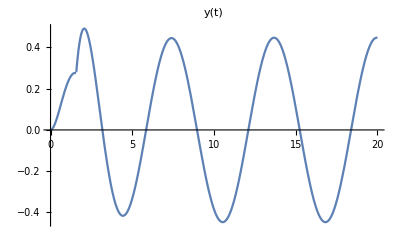

```mathematica
expr=Input["Enter your ODE: \n (ex. y''[t]-2y'[t]+2y[t]==Cos[t]) \n NOTE EXPRESSION MUST BE A FUNCTION OF t"];
degree=Input["How many Initial Conditions do you have?
(Note y[Nunber] and all of it's derivatives count as initial conditions"];
For[n=1,n≤ degree,n++,Input["Condition "<>ToString[n]<>" is:\n (ex. y[0]=2)"]]
LaplaceTransform[expr,t,s];
Solve[%,{LaplaceTransform[y[t],t,s]}];
a=First[%];
"The Laplace Transform Is:"
Apart[LaplaceTransform[y[t],t,s]/.a]
b=InverseLaplaceTransform[%,s,t];
"y(t) Is:" 
 FullSimplify[TrigReduce[FullSimplify[b]]]
Plot[%,{t,0,20},PlotLabel->HoldForm[y [t]]]
```